```mathematica
(*N = n + iϰ*)
```

```mathematica
(*Дисперсия показателя преломления n*)
```

```mathematica
L=1/(λ^2-0.028)
A=3.41696
B=0.138497
C1=0.013924
D1=-0.0000209
E1=0.000000148
n=A+B L+C1 L^2+D1 λ^2+E1 λ^4
```

1/(-0.028+λ^2)

3.41696

0.138497

0.013924

-0.0000209

1.48×10^-7

3.41696-0.0000209 λ^2+1.48×10^-7 λ^4+0.013924/((-0.028+λ^2)^2)+0.138497/(-0.028+λ^2)

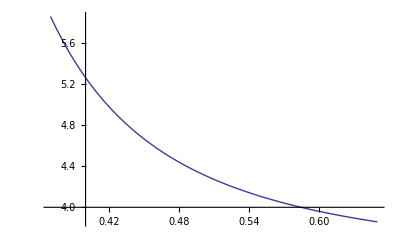

```mathematica
Plot[n,{λ,0.37,0.65},PlotRange->All]
```

```mathematica
(*Дисперсия показателя поглощения ϰ*)
```

```mathematica
λ1=0.3757
ϰ1=1.32
λ2=0.589
ϰ2=0.030104
Solve[{Ko λ1^2/(λ1^2-λ0^2)^2==ϰ1,Ko λ2^2/(λ2^2-λ0^2)^2==ϰ2},{Ko,λ0}]
```

0.3757

1.32

0.589

0.030104

{{Ko→0.00305689,λ0→-0.399037},{Ko→0.00305689,λ0→0.399037},{Ko→0.00449923,λ0→-0.345277},{Ko→0.00449923,λ0→0.345277}}

```mathematica
Ko=0.0045
λ0=0.345277
```

0.0045

0.345277

```mathematica
ϰ=Ko λ^2/(λ^2-λ0^2)^2
```

(0.0045 λ^2)/((-0.119216+λ^2)^2)

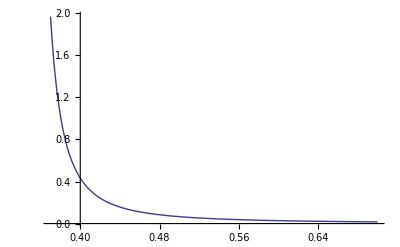

```mathematica
Plot[ϰ,{λ,0.37,0.7},PlotRange->All]
```

```mathematica
λ=0.589
ϰ
```

0.589

0.3757

1.32023

0.0301092